```mathematica
(*Ixx*)
```

```mathematica
Integrate[r*Cos[p]*Sin[t]*r*Cos[p]*Sin[t]*r^2/r^4*Sin[t],{t,0,Pi},{p,0,2Pi}]
```

(4 π)/3

```mathematica
(*Iyy*)
```

```mathematica
Integrate[r*Cos[p]*Sin[t]*r*Cos[p]*Sin[t]*r^2*Sin[t]/r^4,{t,0,Pi},{p,0,2Pi}]
```

(4 π)/3

```mathematica
(*Izz*)
```

```mathematica
Integrate[r^2Cos[t]^2*r^2*Sin[t]/r^4,{t,0,Pi},{p,0,2Pi}]
```

(4 π)/3

```mathematica
(*Ixy*)
```

```mathematica
Integrate[r*Cos[p]*Sin[t]*r*Sin[p]*Sin[t]*r^2/r^4*Sin[t],{t,0,Pi},{p,0,2Pi}]
```

0

```mathematica
(*Iyz*)
```

```mathematica
Integrate[r*Cos[t]*r*Sin[p]*Sin[t]*r^2/r^4*Sin[t],{t,0,Pi},{p,0,2Pi}]
```

0

```mathematica
(*Ixz*)
```

```mathematica
Integrate[r*Cos[t]*r*Sin[p]*Cos[t]*r^2/r^4*Sin[t],{t,0,Pi},{p,0,2Pi}]
```

0

```mathematica
(*Dipole stuff... regularization is needed, i.e. I won't do the integral over r. Suffices to integrate over angles*)
```

```mathematica
(*xx*)
```

```mathematica
Integrate[(3*Cos[p]*Sin[t]*Cos[p]*Sin[t]-1)/r*Sin[t],{t,0,Pi},{p,0,2Pi}]
```

0

```mathematica
(*yy*)
```

```mathematica
Integrate[(3*Sin[p]*Sin[t]*Sin[p]*Sin[t]-1)/r*Sin[t],{t,0,Pi},{p,0,2Pi}]
```

0

```mathematica
(*zz*)
```

```mathematica
Integrate[(3*Cos[t]Cos[t]-1)/r*Sin[t],{t,0,Pi},{p,0,2Pi}]
```

0

```mathematica
(*xy*)
```

```mathematica
Integrate[(3*Cos[p]*Sin[t]*Sin[p]*Sin[t])/r*Sin[t],{t,0,Pi},{p,0,2Pi}]
```

0

```mathematica
(*yz*)
```

```mathematica
Integrate[(3*Cos[t]*Sin[t]*Sin[p])/r*Sin[t],{t,0,Pi},{p,0,2Pi}]
```

0

```mathematica
(*xz*)
```

```mathematica
Integrate[(3*Cos[t]*Cos[p]*Sin[t])/r*Sin[t],{t,0,Pi},{p,0,2Pi}]
```

0

```mathematica
Sqrt[(II-m+1/2)(II+m-1/2+1)(1/2+1/2)(1/2-1/2+1)]
```

√((1/2+II-m) (1/2+II+m))

```mathematica
Sqrt[(II+m-1/2)(II-m+1/2+1)(1/2+1/2)(1/2-1/2+1)]
```

√((3/2+II-m) (-1/2+II+m))

```mathematica
H={{(gJ*muB/2-gI*muB* (m-1/2)) Bz +ah*(m-1/2)/2,ah/2*Sqrt[(II-m+1/2)(II+m+1/2)]},{ah/2*Sqrt[(II-m+1/2)(II+m+1/2)],(-gJ*muB/2-gI*muB* (m+1/2)) Bz-ah*(m+1/2)/2}};
```

```mathematica
Eigenvalues[H]//FullSimplify
```

{1/4 (-ah-4 Bz gI m muB-√((ah+2 ah II)^2+8 ah Bz (gI+gJ) m muB+4 Bz^2 (gI+gJ)^2 muB^2)),1/4 (-ah-4 Bz gI m muB+√((ah+2 ah II)^2+8 ah Bz (gI+gJ) m muB+4 Bz^2 (gI+gJ)^2 muB^2))}

```mathematica
√((ah+2 ah II)^2+8 ah Bz (gI+gJ) m muB+4 Bz^2 (gI+gJ)^2 muB^2)/(ah*(II+1/2))//FullSimplify
```

(2 √((ah+2 ah II)^2+8 ah Bz (gI+gJ) m muB+4 Bz^2 (gI+gJ)^2 muB^2))/(ah+2 ah II)

```mathematica
i=3/2;
```

```mathematica
ah=6.835/2*10^9*6.626*10^(-34);
```

```mathematica
gI=0.0009954;
```

```mathematica
gJ=2.002331;
```

```mathematica
gJ/gI
```

2011.58

```mathematica
B0=(ah*(i+1/2))/((gJ+gI)*muB)
```

0.243765

```mathematica
muB=9.274009994*10^(-24);
```

```mathematica
x[B_]:=(gI+gJ)*muB*B/(ah*(i+1/2));
```

```mathematica
EmFPlus[B_,mF_]:=-ah/4-mF*gI*muB*B+ah*(i+1/2)/2*Sqrt[1+2*mF*x[B]/(i+1/2)+x[B]^2]
```

```mathematica
EStretched[B_,mF_]:=-ah/4-mF*gI*muB*B+ah*(i+1/2)/2*(1-x[B]);
```

```mathematica
EmFMinus[B_,mF_]:=-ah/4-mF*gI*muB*B-ah*(i+1/2)/2*Sqrt[1+2*mF*x[B]/(i+1/2)+x[B]^2]
```

```mathematica
BEnd=1;
```

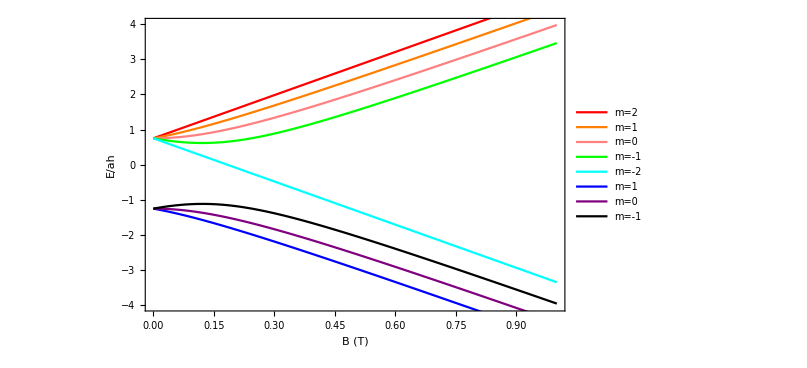

```mathematica
Show[
Plot[EmFPlus[B,2]/ah,{B,0,BEnd},PlotStyle->{Red},PlotLegends->{"m=2"}],
Plot[EmFPlus[B,1]/ah,{B,0,BEnd},PlotStyle->{Orange},PlotLegends->{"m=1"}],
Plot[EmFPlus[B,0]/ah,{B,0,BEnd},PlotStyle->{Pink},PlotLegends->{"m=0"}],
Plot[EmFPlus[B,-1]/ah,{B,0,BEnd},PlotStyle->{Green},PlotLegends->{"m=-1"}],
Plot[EStretched[B,-2]/ah,{B,0,BEnd},PlotStyle->{Cyan},PlotLegends->{"m=-2"}],
Plot[EmFMinus[B,1]/ah,{B,0,BEnd},PlotStyle->{Blue},PlotLegends->{"m=1"}],
Plot[EmFMinus[B,0]/ah,{B,0,BEnd},PlotStyle->{Purple},PlotLegends->{"m=0"}],
Plot[EmFMinus[B,-1]/ah,{B,0,BEnd},PlotStyle->{Black},PlotLegends->{"m=-1"}],
PlotRange->{-4,4},
Frame->True,
FrameLabel->{"B (T)","E/ah"},
AxesOrigin->{0,0}]
```

```mathematica
BEnd=40000;
```

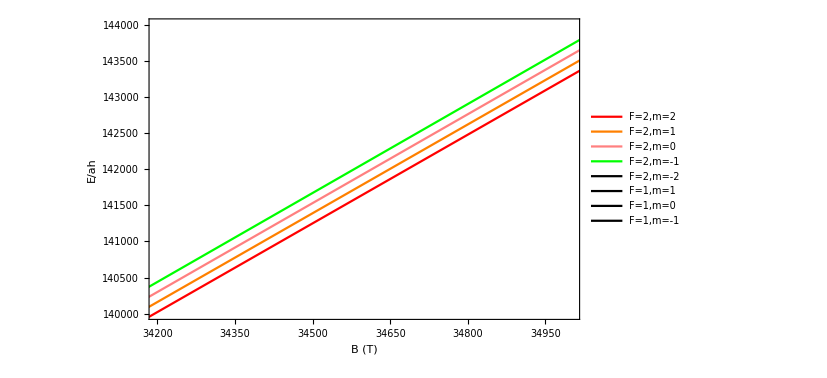

```mathematica
Show[
Plot[EmFPlus[B,2]/ah,{B,0,BEnd},PlotStyle->{Red},PlotLegends->{"F=2,m=2"}],
Plot[EmFPlus[B,1]/ah,{B,0,BEnd},PlotStyle->{Orange},PlotLegends->{"F=2,m=1"}],
Plot[EmFPlus[B,0]/ah,{B,0,BEnd},PlotStyle->{Pink},PlotLegends->{"F=2,m=0"}],
Plot[EmFPlus[B,-1]/ah,{B,0,BEnd},PlotStyle->{Green},PlotLegends->{"F=2,m=-1"}],
Plot[EStretched[B,-2]/ah,{B,0,BEnd},PlotStyle->{Black},PlotLegends->{"F=2,m=-2"}],
Plot[EmFMinus[B,1]/ah,{B,0,BEnd},PlotStyle->{Black},PlotLegends->{"F=1,m=1"}],
Plot[EmFMinus[B,0]/ah,{B,0,BEnd},PlotStyle->{Black},PlotLegends->{"F=1,m=0"}],
Plot[EmFMinus[B,-1]/ah,{B,0,BEnd},PlotStyle->{Black},PlotLegends->{"F=1,m=-1"}],
Frame->True,
PlotRange->{{34200,35000},{140000,144000}},
FrameLabel->{"B (T)","E/ah"},
AxesOrigin->{0,0}]
```

```mathematica
BEnd=400;
```

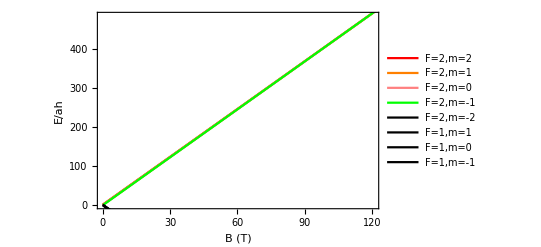

```mathematica
Show[
Plot[EmFPlus[B,2]/ah,{B,0,BEnd},PlotStyle->{Red},PlotLegends->{"F=2,m=2"}],
Plot[EmFPlus[B,1]/ah,{B,0,BEnd},PlotStyle->{Orange},PlotLegends->{"F=2,m=1"}],
Plot[EmFPlus[B,0]/ah,{B,0,BEnd},PlotStyle->{Pink},PlotLegends->{"F=2,m=0"}],
Plot[EmFPlus[B,-1]/ah,{B,0,BEnd},PlotStyle->{Green},PlotLegends->{"F=2,m=-1"}],
Plot[EStretched[B,-2]/ah,{B,0,BEnd},PlotStyle->{Black},PlotLegends->{"F=2,m=-2"}],
Plot[EmFMinus[B,1]/ah,{B,0,BEnd},PlotStyle->{Black},PlotLegends->{"F=1,m=1"}],
Plot[EmFMinus[B,0]/ah,{B,0,BEnd},PlotStyle->{Black},PlotLegends->{"F=1,m=0"}],
Plot[EmFMinus[B,-1]/ah,{B,0,BEnd},PlotStyle->{Black},PlotLegends->{"F=1,m=-1"}],
Frame->True,
PlotRange->{{0,120.5},{0,485}},
FrameLabel->{"B (T)","E/ah"},
AxesOrigin->{0,0}]
```

```mathematica
BEnd=2000000;
```

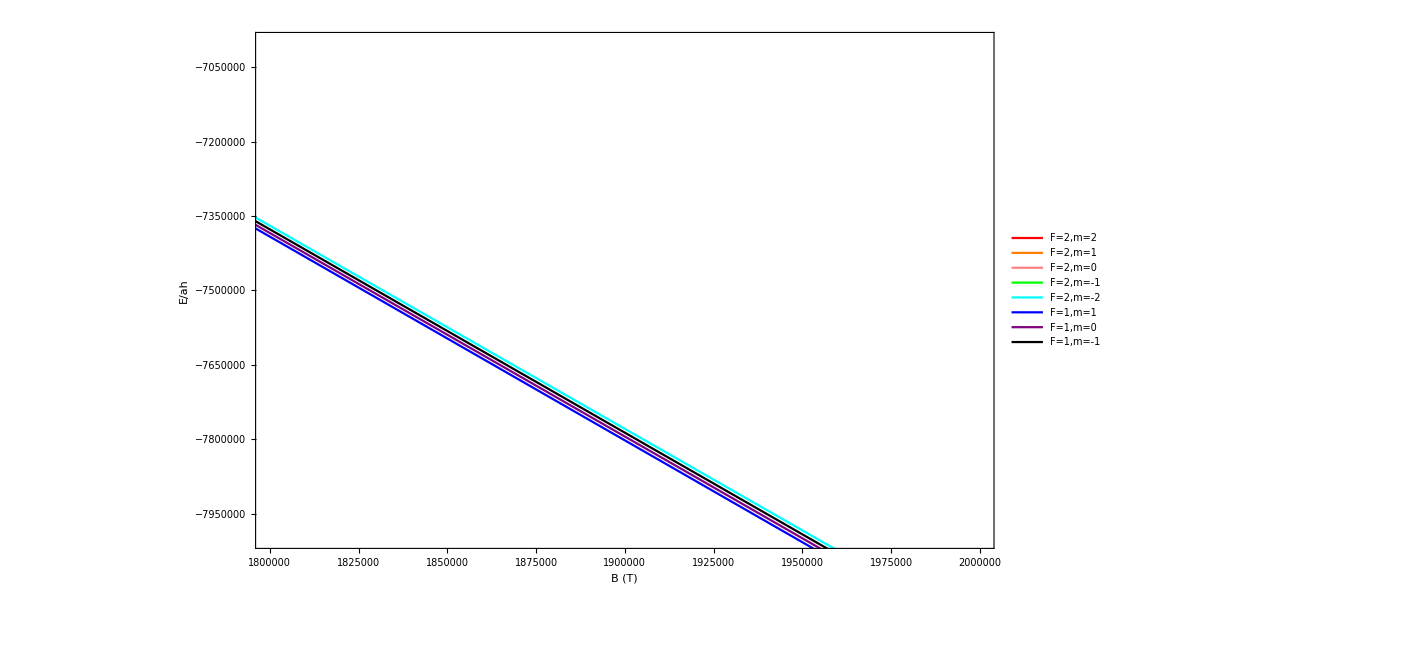

```mathematica
Show[
Plot[EmFPlus[B,2]/ah,{B,0,BEnd},PlotStyle->{Red},PlotLegends->{"F=2,m=2"}],
Plot[EmFPlus[B,1]/ah,{B,0,BEnd},PlotStyle->{Orange},PlotLegends->{"F=2,m=1"}],
Plot[EmFPlus[B,0]/ah,{B,0,BEnd},PlotStyle->{Pink},PlotLegends->{"F=2,m=0"}],
Plot[EmFPlus[B,-1]/ah,{B,0,BEnd},PlotStyle->{Green},PlotLegends->{"F=2,m=-1"}],
Plot[EStretched[B,-2]/ah,{B,0,BEnd},PlotStyle->{Cyan},PlotLegends->{"F=2,m=-2"}],
Plot[EmFMinus[B,1]/ah,{B,0,BEnd},PlotStyle->{Blue},PlotLegends->{"F=1,m=1"}],
Plot[EmFMinus[B,0]/ah,{B,0,BEnd},PlotStyle->{Purple},PlotLegends->{"F=1,m=0"}],
Plot[EmFMinus[B,-1]/ah,{B,0,BEnd},PlotStyle->{Black},PlotLegends->{"F=1,m=-1"}],
Frame->True,
PlotRange->{{1800000,2000000},{-8000000,-7000000}},
FrameLabel->{"B (T)","E/ah"},
AxesOrigin->{0,0}]
```

```mathematica
(*Part (c)*)
```

```mathematica
i=3/2;
```

```mathematica
ah=6.835/2*10^9*6.626*10^(-34);
```

```mathematica
gI=0.0009954;
```

```mathematica
gJ=2.002331;
```

```mathematica
muB=9.274009994*10^(-24);
```

```mathematica
B0=(ah*(i+1/2))/((gJ+gI)*muB)
```

0.243765

```mathematica
F=3/2+1/2;
```

```mathematica
EmFPlusF[mF_]:=-ah/4-mF*gI*muB*x*B0+ah*F/2*Sqrt[1+2*mF*x/F+x^2]
```

```mathematica
EmFMinusF[mF_]:=-ah/4-mF*gI*muB*x*B0-ah*F/2*Sqrt[1+2*mF*x/F+x^2]
EStretchedF[mF_]:=-ah/4-mF*gI*muB*x*B0+ah*(i+1/2)/2*(1-x);
```

```mathematica
EStretchedFHigh[mF_]:=-ah/4-mF*gI*muB*x*B0+ah*(i+1/2)/2*(1+x);
```

```mathematica
(*mF=2,mF=1*)
```

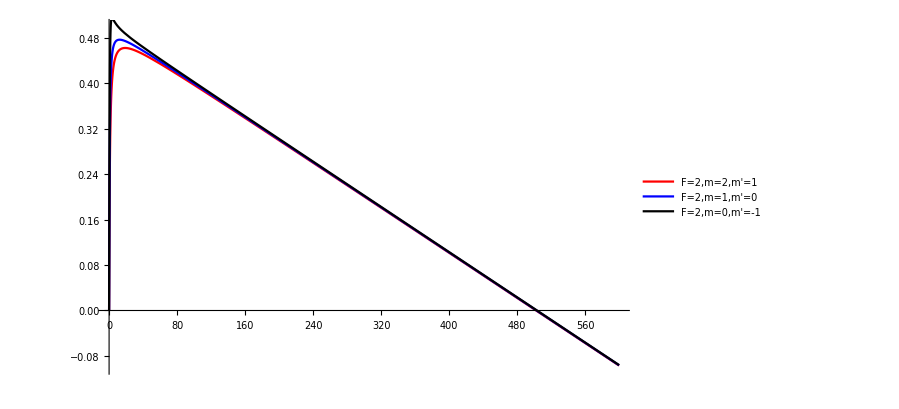

```mathematica
Show[Plot[EmFPlusF[2]/ah-EmFPlusF[1]/ah,{x,0,600},PlotStyle->{Red},PlotLegends->{"F=2,m=2,m'=1"}],
Plot[EmFPlusF[1]/ah-EmFPlusF[0]/ah,{x,0,600},PlotStyle->{Blue},PlotLegends->{"F=2,m=1,m'=0"}],
Plot[EmFPlusF[0]/ah-EmFPlusF[-1]/ah,{x,0,600},PlotStyle->{Black},PlotLegends->{"F=2,m=0,m'=-1"}],
PlotRange->{{0,600},{-0.1,0.5}}]
```

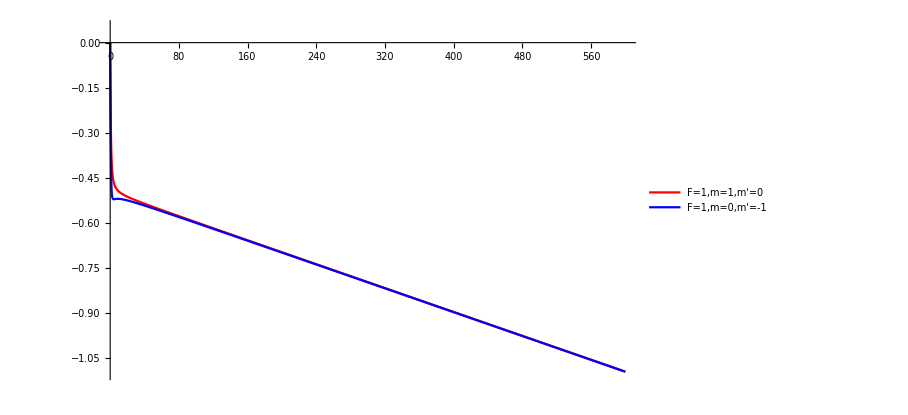

```mathematica
Show[Plot[EmFMinusF[1]/ah-EmFMinusF[0]/ah,{x,0,600},PlotStyle->{Red},PlotLegends->{"F=1,m=1,m'=0"}],
Plot[EmFMinusF[0]/ah-EmFMinusF[-1]/ah,{x,0,600},PlotStyle->{Blue},PlotLegends->{"F=1,m=0,m'=-1"}],
PlotRange->{{0,600},{-1.1,0.05}}]
```

```mathematica
(*Within top manifold*)
```

```mathematica
Series[EmFPlusF[2]/ah-EmFPlusF[1]/ah/.{x->x0+dx},{dx,0,2}]//FullSimplify
```

-(0.375 dx^2)/((1+x0+x0^2)^(3/2))+O[dx]^3

```mathematica
Series[EmFPlusF[1]/ah-EmFPlusF[0]/ah/.{x->x0+dx},{dx,0,1}]//FullSimplify
```

-0.25-(1. x0 dx)/(√(1+x0^2))+O[dx]^2

```mathematica
Series[EmFPlusF[0]/ah-EmFPlusF[-1]/ah/.{x->x0+dx},{dx,0,1}]//FullSimplify
```

0.25+(1. x0 dx)/(√(1+x0^2))+O[dx]^2

```mathematica
Series[EmFPlusF[-1]/ah-EStretchedF[-2]/ah/.{x->x0+dx},{dx,0,1}]//FullSimplify
```

(-1.+0.998013 x0)+0.998013 dx+O[dx]^2

```mathematica
(*Within bottom manifold*)
```

```mathematica
Series[EmFMinusF[1]/ah-EmFMinusF[0]/ah/.{x->x0+dx},{dx,0,1}]//FullSimplify
```

-0.25+(1. x0 dx)/(√(1+x0^2))+O[dx]^2

```mathematica
Series[EmFMinusF[0]/ah-EmFMinusF[-1]/ah/.{x->x0+dx},{dx,0,1}]//FullSimplify
```

0.25-(1. x0 dx)/(√(1+x0^2))+O[dx]^2

```mathematica
(*Between manifolds: notation = mF low to mF high*)
```

```mathematica
Series[EmFMinusF[-1]/ah-EStretchedF[-2]/ah/.{x->x0+dx},{dx,0,1}]//FullSimplify
```

(-1.+0.998013 x0)+0.998013 dx+O[dx]^2

```mathematica
Series[EmFMinusF[-1]/ah-EmFPlusF[-1]/ah/.{x->x0+dx},{dx,0,2}]//FullSimplify
```

-(0.75 dx^2)/(1+(-1+x0) x0)^(3/2)+O[dx]^3

```mathematica
Series[EmFMinusF[-1]/ah-EmFPlusF[0]/ah/.{x->x0+dx},{dx,0,1}]//FullSimplify
```

-0.25-(1. x0 dx)/(√(1+x0^2))+O[dx]^2

```mathematica
Series[EmFMinusF[0]/ah-EmFPlusF[-1]/ah/.{x->x0+dx},{dx,0,1}]//FullSimplify
```

0.25-(1. x0 dx)/(√(1+x0^2))+O[dx]^2

```mathematica
Series[EmFMinusF[0]/ah-EmFPlusF[0]/ah/.{x->x0+dx},{dx,0,1}]//FullSimplify
```

-(2. x0 dx)/(√(1+x0^2))+O[dx]^2

```mathematica
Series[EmFMinusF[0]/ah-EmFPlusF[1]/ah/.{x->x0+dx},{dx,0,1}]//FullSimplify
```

0.25-(1. x0 dx)/(√(1+x0^2))+O[dx]^2

```mathematica
Series[EmFMinusF[1]/ah-EmFPlusF[0]/ah/.{x->x0+dx},{dx,0,1}]//FullSimplify
```

-0.25-(1. x0 dx)/(√(1+x0^2))+O[dx]^2

```mathematica
Series[EmFMinusF[1]/ah-EmFPlusF[1]/ah/.{x->x0+dx},{dx,0,2}]//FullSimplify
```

-(0.75 dx^2)/((1+x0+x0^2)^(3/2))+O[dx]^3

```mathematica
Series[EmFMinusF[1]/ah-EStretchedFHigh[2]/ah/.{x->x0+dx},{dx,0,1}]//FullSimplify
```

(-1.-0.998013 x0)-0.998013 dx+O[dx]^2

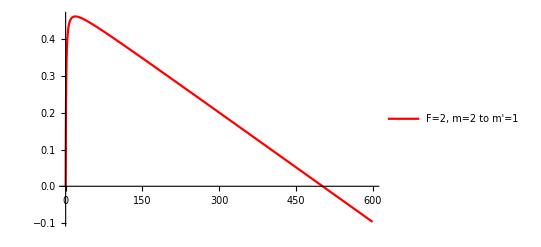

```mathematica
Plot[EmFPlusF[2]/ah-EmFPlusF[1]/ah,{x,0,600},PlotStyle->{Red},PlotLegends->{"F=2, m=2 to m'=1"}]
```

```mathematica
EmFPlusF[2]/ah-EmFPlusF[1]/ah//FullSimplify
```

-0.000993747 x+1. √((1+x)^2)-1. √(1+x+x^2)

```mathematica
D[-0.0009937471996575298 x+1. √((1+x)^2)-1. √(1+x+x^2),x]//FullSimplify
```

-0.000993747+(1. (1+x))/(√((1+x)^2))-(0.5 (1+2 x))/(√(1+x+x^2))

```mathematica
Solve[-0.0009937471996575298+(1. (1+x))/(√((1+x)^2))-(0.5 (1+2 x))/(√(1+x+x^2))==0,x]
```

{{x→18.9113}}

```mathematica
18.9113*B0
```

4.60991

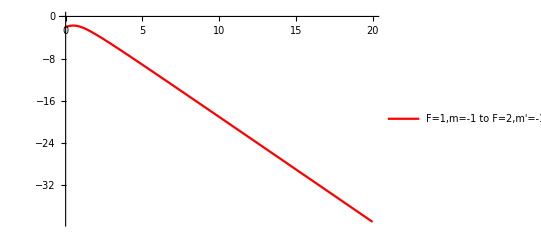

```mathematica
Plot[EmFMinusF[-1]/ah-EmFPlusF[-1]/ah,{x,0,20},PlotStyle->{Red},PlotLegends->{"F=1,m=-1 to F=2,m'=-1"}]
```

```mathematica
EmFMinusF[-1]/ah-EmFPlusF[-1]/ah//FullSimplify
```

-2. √(1+(-1+x) x)

```mathematica
D[-2. √(1+(-1+x) x),x]
```

-(1. (-1+2 x))/(√(1+(-1+x) x))

```mathematica
Solve[-(1. (-1+2 x))/(√(1+(-1+x) x))==0,x]
```

{{x→0.5}}

```mathematica
0.5*B0
```

0.121882

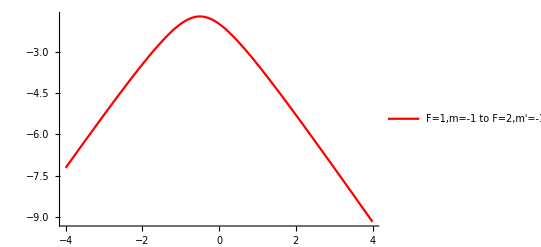

```mathematica
Plot[EmFMinusF[1]/ah-EmFPlusF[1]/ah,{x,-4,4},PlotStyle->{Red},PlotLegends->{"F=1,m=-1 to F=2,m'=-1"}]
```

```mathematica
EmFMinusF[1]/ah-EmFPlusF[1]/ah//FullSimplify
```

-2. √(1+x+x^2)

```mathematica
D[-2. √(1+x+x^2),x]
```

-(1. (1+2 x))/(√(1+x+x^2))

```mathematica
Solve[-(1. (1+2 x))/(√(1+x+x^2))==0,x]
```

{{x→-0.5}}

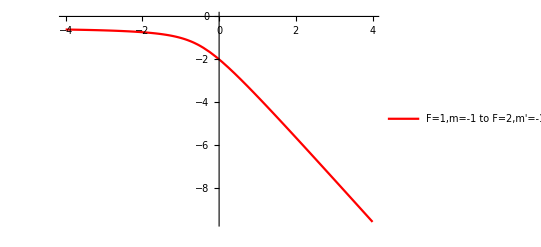

```mathematica
Plot[EmFMinusF[1]/ah-EStretchedFHigh[2]/ah,{x,-4,4},PlotStyle->{Red},PlotLegends->{"F=1,m=-1 to F=2,m'=-1"}]
```

```mathematica
EmFMinusF[1]/ah-EStretchedFHigh[2]/ah//FullSimplify
```

-1.-0.999006 x-1. √(1+x+x^2)

```mathematica
D[-1.-0.9990062528003425 x-1. √(1+x+x^2),x]//FullSimplify
```

-0.999006-(0.5 (1+2 x))/(√(1+x+x^2))

```mathematica
Solve[-0.9990062528003425-(0.5 (1+2 x))/(√(1+x+x^2))==0,x]
```

{{x→-19.9113}}

```mathematica
(*Part (d)*)
```

```mathematica
Series[EmFMinusF[-1]/ah-EmFPlusF[1]/ah/.{x->x0+dx},{dx,0,2}]//FullSimplify//TeXForm
```

\text{dx}^2 \left(-\frac{0.375}{\left(\text{x0}^2+\text{x0}+1\right)^{3/2}}-\frac{0.375}{((\text{x0}-1) \text{x0}+1)^{3/2}}\right)+O\left(\text{dx}^3\right)

```mathematica
EmFMinusF[-1]/ah-EmFPlusF[1]/ah//FullSimplify
```

0.00198749 x-1. √(1+(-1+x) x)-1. √(1+x+x^2)

```mathematica
EmFMinusF[-1]-EmFPlusF[1]/.{x->0.0000125}
```

-4.52887×10^-24

```mathematica
4.528870944008454*^-24/ah
```

2.

```mathematica
0.03/(0.24*10000)
```

0.0000125

```mathematica
dEdx=D[0.0019874943993150596 x-1. √(1+(-1+x) x)-1. √(1+x+x^2),x]//FullSimplify
```

0.00198749+(0.5-1. x)/(√(1+(-1+x) x))-(0.5 (1+2 x))/(√(1+x+x^2))

```mathematica
Solve[0.0019874943993150596+(0.5-1. x)/(√(1+(-1+x) x))-(0.5 (1+2 x))/(√(1+x+x^2))==0,x]
```

{{x→0.001325}}

```mathematica
0.001324995975439117*B0
```

0.000322987

```mathematica
0.0003229871436506178*10^4
```

3.22987

```mathematica
dEdx/.{x->0}
```

0.00198749

```mathematica
B0
```

0.243765

```mathematica
1/B0*ah*0.001987494399315004*0.03/(10000)
```

5.53881×10^-32

```mathematica
5.538809728816407*^-32/(6.626*10^(-34))
```

83.5921

```mathematica
1*ah/(6.626*10^(-34))
```

3.4175×10^9

```mathematica
dE2dx2=D[0.0019874943993150596 x-1. √(1+(-1+x) x)-1. √(1+x+x^2),{x,2}]/.{x->0.001325}
```

-1.5

```mathematica
(1/B0^2)*(0.03/10000)^2(1/2)*1.5*ah
```

2.5723×10^-34

```mathematica
2.5723044812493337*^-34/(6.626*10^(-34))
```

0.388214